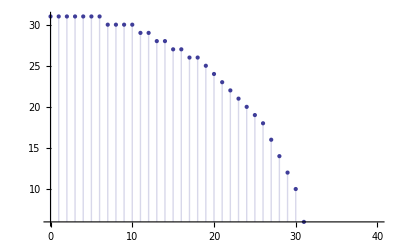

```mathematica
DiscretePlot[Floor[(1000-j^2)^(1/2)],{j,0,40}]
```

```mathematica
Integrate[1,{t,0,x^(1/2)}]
```

√x

```mathematica
Integrate[1,{t,0,x^(1/2)},{u,0,(x-t^2)^(1/2)}]
```

(π x)/4

```mathematica
Integrate[1,{t,0,x^(1/2)},{u,0,(x-t^2)^(1/2)},{v,0,(x-t^2-u^2)^(1/2)}]
```

1/6 π x^(3/2)

```mathematica
Integrate[1,{t,0,x^(1/2)},{u,0,(x-t^2)^(1/2)},{v,0,(x-t^2-u^2)^(1/2)},{w,0,(x-t^2-u^2-v^2)^(1/2)}]
```

(π^2 x^2)/32

```mathematica
Integrate[1,{t,0,x^(1/2)},{u,0,(x-t^2)^(1/2)},{v,0,(x-t^2-u^2)^(1/2)},{w,0,(x-t^2-u^2-v^2)^(1/2)},{y,0,(x-t^2-u^2-v^2-w^2)^(1/2)}]
```

1/60 π^2 x^(5/2)

```mathematica
Table[Gamma[j/2],{j,1,10}]
```

{√π,1,(√π)/2,1,(3 √π)/4,2,(15 √π)/8,6,(105 √π)/16,24}

```mathematica
val[r_,n_]:=Pi^(n/2)/Gamma[1+n/2]r^n
val2[r_,n_]:=Pi^(n/2)/Gamma[1+n/2]r^(n/2)/2^n
val3[n_,k_]:=(2^-k n^(k/2) π^(k/2))/Gamma[1+k/2]
val4[n_,k_]:=(2^-k (π n)^(k/2))/((k/2)!)
val5[n_,k_]:=(n π/4)^k/(k!)
val6[n_,k_]:=((π n)/4)^(k/2)/((k/2)!)
```

```mathematica
val[n^(1/2),3]/2^3
```

1/6 n^(3/2) π

```mathematica
val6[n,6]
```

(n^3 π^3)/384

```mathematica
Table[val5[n,k],{k,0,6}]
```

{1,(n π)/4,(n^2 π^2)/32,(n^3 π^3)/384,(n^4 π^4)/6144,(n^5 π^5)/122880,(n^6 π^6)/2949120}

```mathematica
Sum[Binomial[z,k]((π n)/4)^(k/2)/((k/2)!),{k,0,Infinity}]
```

√n z HypergeometricPFQ[{1/2-z/2,1-z/2},{3/2,3/2},(n π)/4]+HypergeometricPFQ[{1/2-z/2,-z/2},{1/2,1},(n π)/4]

```mathematica
FullSimplify@Sum[(-1)^(k+1)/k ((π n)/4)^(k/2)/((k/2)!),{k,1,Infinity}]
```

1/2 (EulerGamma+Gamma[0,-(n π)/4]+2 √n HypergeometricPFQ[{1/2,1},{3/2,3/2},(n π)/4]+Log[-(n π)/4])

```mathematica
Sum[Binomial[z,k](n π/4)^k/(k!),{k,0,Infinity}]
```

Hypergeometric1F1[-z,1,-(n π)/4]

```mathematica
FullSimplify@Sum[(-1)^(k+1)/k(n π/4)^k/(k!),{k,1,Infinity}]
```

EulerGamma+Gamma[0,(n π)/4]+Log[(n π)/4]

```mathematica
Clear[C2]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
C2[n_,0]:=UnitStep[n]
C2[n_,k_]:=C2[n,k]=Sum[C2[n-j^2,k-1],{j,1,Floor[n^(1/2)]}]
C2f[n_,k_]:=C2[n,2k]
dC2f[n_,k_]:=C2[n,2k]-C2[n-1,2k]
Cz[n_,z_]:=Sum[bin[z,k]C2[n,2k],{k,0,n/2+1}]
Cza[n_,z_]:=Sum[bin[z,k]C2[n,k],{k,0,n}]
aprox[n_,k_]:=(n π/4)^k/(k!)
aproxz[n_,z_]:=Hypergeometric1F1[-z,1,-(n π)/4]
```

```mathematica
Table[{n,C2f[n,1]},{n,1,40}]//TableForm
```

```mathematica
C2f[18.,3]
```

93

```mathematica
aprox[18.,3]
```

470.908

```mathematica
Cz[18.,3]
```

259

```mathematica
aproxz[18.,3]
```

814.109

```mathematica
D[(n π/4)^k/(k!),k]/.k->0
```

EulerGamma+Log[n]+Log[π/4]

```mathematica
D[(n π/4)^k/(k!),n]
```

(k n^(-1+k) (π/4)^k)/(k!)

```mathematica
Table[{n,n/2 D[Cz[n,z]-Cz[n-1,z],z]/.z->0},{n,1,64}]//TableForm
```

```mathematica
Table[{n,FullSimplify[Cz[n,1]-Cz[n-1,1]]},{n,1,40}]//TableForm
```

```mathematica
Table[{n,N@(π/4),N@C2f[n,1]/n},{n,13501,13540}]//TableForm
```

13501 | 0.785398 | 0.776831
13502 | 0.785398 | 0.776774
13503 | 0.785398 | 0.776716
13504 | 0.785398 | 0.776659
13505 | 0.785398 | 0.777194
13506 | 0.785398 | 0.777136
13507 | 0.785398 | 0.777079
13508 | 0.785398 | 0.777021
13509 | 0.785398 | 0.776964
13510 | 0.785398 | 0.776906
13511 | 0.785398 | 0.776848
13512 | 0.785398 | 0.776791
13513 | 0.785398 | 0.776882
13514 | 0.785398 | 0.77712
13515 | 0.785398 | 0.777063
13516 | 0.785398 | 0.777005
13517 | 0.785398 | 0.776948
13518 | 0.785398 | 0.77689
13519 | 0.785398 | 0.776833
13520 | 0.785398 | 0.777219
13521 | 0.785398 | 0.777161
13522 | 0.785398 | 0.777252
13523 | 0.785398 | 0.777194
13524 | 0.785398 | 0.777137
13525 | 0.785398 | 0.777523
13526 | 0.785398 | 0.777466
13527 | 0.785398 | 0.777408
13528 | 0.785398 | 0.777351
13529 | 0.785398 | 0.777293
13530 | 0.785398 | 0.777236
13531 | 0.785398 | 0.777178
13532 | 0.785398 | 0.777121
13533 | 0.785398 | 0.777063
13534 | 0.785398 | 0.777006
13535 | 0.785398 | 0.776949
13536 | 0.785398 | 0.776891
13537 | 0.785398 | 0.776982
13538 | 0.785398 | 0.776924
13539 | 0.785398 | 0.776867
13540 | 0.785398 | 0.777105

```mathematica
D[aprox[x,1],x]
```

π/4

```mathematica
Table[{n,dC2f[n,1]/n},{n,1,40}]//TableForm
```

```mathematica
(** http://oeis.org/A162552 **)
```

```mathematica
Table[{n,n D[Cza[n,z]-Cza[n-1,z],z]/.z->0},{n,1,64}]//TableForm
```

1 | 1
2 | -1
3 | 1
4 | 3
5 | -4
6 | 5
7 | -6
8 | 3
9 | 10
10 | -16
11 | 23
12 | -27
13 | 14
14 | 6
15 | -34
16 | 83
17 | -101
18 | 86
19 | -37
20 | -72
21 | 204
22 | -309
23 | 346
24 | -243
25 | -29
26 | 454
27 | -908
28 | 1214
29 | -1130
30 | 470
31 | 776
32 | -2413
33 | 3884
34 | -4421
35 | 3244
36 | 162
37 | -5438
38 | 11285
39 | -15352
40 | 14688
41 | -6887
42 | -8640
43 | 29241
44 | -48353
45 | 56270
46 | -42850
47 | 1834
48 | 63965
49 | -138529
50 | 192709
51 | -189566
52 | 97022
53 | 94182
54 | -353398
55 | 600728
56 | -714970
57 | 565916
58 | -68934
59 | -749653
60 | 1699518
61 | -2418832
62 | 2441404
63 | -1350570
64 | -999405

```mathematica
D[(Pi/4 x)^(k/2)/(k/2)!,x]
```

(2^(-1-k) k π^(k/2) x^(-1+k/2))/(k/2!)

```mathematica
D[x^(1/2),x]
```

1/(2 √x)

```mathematica
val7[n_,k_]:=((π n)/4)^(k/2)/((k/2)!)
cz[n_,z_]:=Sum[Binomial[z,k]val7[n,k],{k,0,Infinity}]
```

```mathematica
cz[10.,3.]
```

50.6064

```mathematica
LaguerreL[1.5, -Pi/4 10.]
```

21.3774

```mathematica
cz[x,z]
```

√x z HypergeometricPFQ[{1/2-z/2,1-z/2},{3/2,3/2},(π x)/4]+HypergeometricPFQ[{1/2-z/2,-z/2},{1/2,1},(π x)/4]

```mathematica
CoefficientList[Series[Log[Sum[x^(n^2),{n,0,Infinity}]],{x,0,20}],x]
```

{0,1,-1/2,1/3,3/4,-4/5,5/6,-6/7,3/8,10/9,-8/5,23/11,-9/4,14/13,3/7,-34/15,83/16,-101/17,43/9,-37/19,-18/5}

```mathematica
Table[ D[Cza[n,z]-Cza[n-1,z],z]/.z->0,{n,0,20}]
```

{0,1,-1/2,1/3,3/4,-4/5,5/6,-6/7,3/8,10/9,-8/5,23/11,-9/4,14/13,3/7,-34/15,83/16,-101/17,43/9,-37/19,-18/5}

```mathematica
Table[ Cza[n,z]-Cza[n-1,z]/.z->2,{n,0,20}]
```

{1,2,1,0,2,2,0,0,1,2,2,0,0,2,0,0,2,2,1,0,2}

```mathematica
CoefficientList[Series[Sum[x^((n)^2),{n,0,Infinity}]^2,{x,0,20}],x]
```

{1,2,1,0,2,2,0,0,1,2,2,0,0,2,0,0,2,2,1,0,2}

```mathematica
Table[ Cza[n,z]-Cza[n-1,z]/.z->-1,{n,0,20}]
```

{1,-1,1,-1,0,1,-2,3,-3,1,2,-6,10,-11,8,0,-14,29,-39,38,-18}

```mathematica
CoefficientList[Series[Sum[x^((n)^2),{n,0,Infinity}]^-1,{x,0,20}],x]
```

{1,-1,1,-1,0,1,-2,3,-3,1,2,-6,10,-11,8,0,-14,29,-39,38,-18}

```mathematica
CoefficientList[Series[Log[Sum[x^((n)^2),{n,0,Infinity}]],{x,0,20}],x]
```

{0,1,-1/2,1/3,3/4,-4/5,5/6,-6/7,3/8,10/9,-8/5,23/11,-9/4,14/13,3/7,-34/15,83/16,-101/17,43/9,-37/19,-18/5}

```mathematica
Table[ D[Cz[n,z]-Cz[n-1,z],z]/.z->0,{n,0,20}]
```

{0,0,1,0,-1/2,2,1/3,-2,3/4,2,-4/5,-2,17/6,2,-34/7,-4/3,51/8,0,-80/9,6,62/5}

```mathematica
Table[ Cz[n,z]-Cz[n-1,z]/.z->1,{n,1,20}]
```

{0,1,0,0,2,0,0,1,0,2,0,0,2,0,0,0,2,1,0,2}

```mathematica
CoefficientList[Series[Sum[(x)^(n^2),{n,0,Infinity}],{x,0,20}],x]
```

{1,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1}

```mathematica
Table[sq[n],{n,1,20}]
```

{0,1,0,0,2,0,0,1,0,2,0,0,2,0,0,0,2,1,0,2}

```mathematica
Table[C2f[n,1]-C2f[n-1,1],{n,1,20}]
```

{0,1,0,0,2,0,0,1,0,2,0,0,2,0,0,0,2,1,0,2}

```mathematica
SquaresR[1,9]
```

2

```mathematica
sq[n_]:=SquaresR[2,n]/4-SquaresR[1,n]/2
```

```mathematica
Series[Sum[ SquaresR[k,n] x^n,{n,0,Infinity}],{x,0,20}]
```

∑_(n=0)^∞ x^n SquaresR[k,n]

```mathematica
CoefficientList[Series[EllipticTheta[2,3,x],{x,0,20}],x]
```

General::poly: 2\ x^1/4\ Cos[3] + 2\ x^9/4\ Cos[9] + 2\ x^25/4\ Cos[15] + 2\ x^49/4\ Cos[21] is not a polynomial.

{2 x^(1/4) Cos[3]+2 x^(9/4) Cos[9]+2 x^(25/4) Cos[15]+2 x^(49/4) Cos[21]}

```mathematica
Sum[x^(n^2),{n,0,Infinity}]
```

1/2 (1+EllipticTheta[3,0,x])